# Single phosphorylation dephosphorylation cycle motif

## The model description

This particular motif describe one phosphorylation-desphosphorylation cycle (can be generalized to any futile cycles) .

K + S ⇌ KS → K + S_p
P + S_p ⇌ PS_p → P + S
∅ → K
K → ∅ 

The above reactions show a simple system that composed of one scaffold protein, one kinase, one phosphatase and one substrate. Here we try to descibe this simple system with differential equation following the mass action kinetics.

ⅆ[K]/ⅆt=-k[1][K][S]+k[2][KS]+k[3][KS]+ k[7]k_d-k_d[K],
ⅆ[P]/ⅆt=-k[4][P][S_p]+k[5][PS_p]+k[6][PS_p],
ⅆ[S]/ⅆt=-k[1][K][S]+k[2][KS]+k[6][PS_p],
ⅆ[S_p]/ⅆt=-k[4][P][S_p]+k[3][KS]+k[5][PS_p],
ⅆ[KS]/ⅆt=k[1][K][S]-k[2][KS]-k[3][KS],
ⅆ[PS_p]/ⅆt=k[4][P][S_p]-k[5][PS_p]-k[6][PS_p].

And the system need to follow these conservation equations:

[K]+[KS]=[K_tot],
[P]+[PS_p]=[P_tot],
[S]+[S_p]+[KS]+[PS_p]=[S_tot],

In the following setion, we will solve the differential equations to understand the dynamics and behaviour of such system.

## Understanding the dynamics of the simple system with input pertubations (numerical study)

Since, it is a bit difficult to solve the differential equations analytically. Here we try to study them numerically. The quantification can be derived from the actually fitness funcitons for ultrasensitive response and adaptive response. Then we save all the parameter sets as well as their score on ultrasensitivity and adaptation.

```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
kd=10;
des={-k[1]* x[1][t] *x[3][t]+k[2]* x[5][t]+k[3] *x[5][t]+k7[t]*kd-kd*x[1][t],-k[4]* x[2][t] *x[4][t]+k[5]* x[6][t]+k[6] *x[6][t],-k[1]* x[1][t] *x[3][t]+k[2] *x[5][t]+k[6]*x[6][t],
-k[4]*x[2][t]* x[4][t]+k[3]*x[5][t]+k[5]* x[6][t],
k[1]* x[1][t] *x[3][t]-k[2] *x[5][t]-k[3]* x[5][t],
k[4] *x[2][t]* x[4][t]-k[5] *x[6][t]-k[6] *x[6][t],0};

init={totK,totP,totS,0,0,0,1.*10^-4};(*init={tot[1],tot[2],tot[3],0.00001,0.00001,0.00001,totT,0.00001,0.00001};*)
```

```mathematica
AbsoluteTiming[
totK=0.0001;totP=0.1;totS=1;
stepNum=5;
sampleSize=10000;

pars={};
vars=Array[x,6];AppendTo[vars,k7];
dvars=Thread[Derivative[1][vars]];
SeedRandom[IntegerPart[SessionTime[]]];
ts={};
For[num=1,num≤sampleSize,num++,
Block[{k,T,ssthreshold},k[n_]:=k[n]=10^(RandomReal[]*6-3);
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
totT=1.*10^(RandomReal[]*4-3);

Block[{tPer,step},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k7[t]->10*k7[t]}]]},vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*((0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.01])))];
];
ad=(ad/0.0001)^(1/(stepNum));

ks=Array[k,6];
AppendTo[pars,Join[ks,{totT,totK,totP,totS,us,ad,num,(ks[[2]]+ks[[3]])/ks[[1]],(ks[[5]]+ks[[6]])/ks[[4]]}]];
];
];
];
];
]

(*Plot@@{{{(x[7][t]+x[8][t]+x[9][t]),x[4][t]}/.sol},Flatten@{t,x[1]["Domain"]/.sol},PlotLegends->{"T_tot","S_p"}}
ListPlot[Transpose@{xT,x4},PlotRange->{0,10}]*)
(*Print[pars];*)
transPars=Transpose[pars];
Export["phoDephoCycleSaturationSampling.csv",transPars];
(*Export["unsaturationSampling.csv",transPars];*)
```

{993.408,Null}

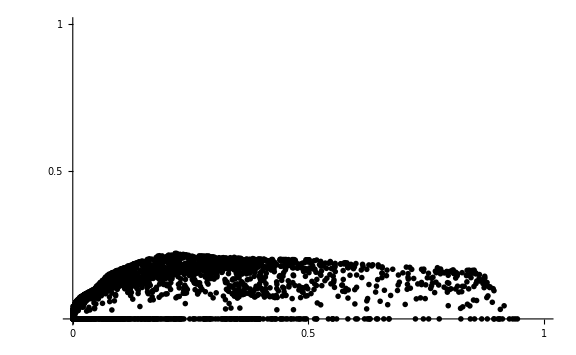

```mathematica
ListPlot[Transpose[{transPars[[11]],transPars[[12]]}],PlotRange->{{0,1},{0,1}},(*AxesLabel->{"Ultrasensitive score","Adaptive score"},*)Ticks->{{0,0.5,1}, {0.5,1}},PlotStyle->{Thick,PointSize[0.01]},PlotTheme->"Monochrome",PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
```

```mathematica
maxAndIndex[a_]:={#,First@SparseArray[UnitStep[a-#]]["AdjacencyLists"]}&@Max@a
```

```mathematica
maxAndIndex[transPars[[11]]]
```

{0.944481,2116}

```mathematica
maxAndIndex[transPars[[12]]]
```

{0.222025,3655}

```mathematica
usIndex=maxAndIndex[transPars[[11]]]//Last;
adIndex=maxAndIndex[transPars[[12]]]//Last;
pars[[usIndex]]
```

{0.0802404,240.956,2.02589,0.00930462,19.116,0.00339675,0.448252,0.0001,0.1,1,0.944481,0.,3015,3028.17,2054.83}

```mathematica
pars[[adIndex]]
```

{0.111416,0.00343489,0.00240456,0.0343359,0.0195006,534.276,0.181642,0.0001,0.1,1,0.217528,0.222025,5182,0.0524114,15560.8}

```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
kd=10;
des={-k[1]* x[1][t] *x[3][t]+k[2]* x[5][t]+k[3] *x[5][t]+k7[t]*kd-kd*x[1][t],-k[4]* x[2][t] *x[4][t]+k[5]* x[6][t]+k[6] *x[6][t],-k[1]* x[1][t] *x[3][t]+k[2] *x[5][t]+k[6]*x[6][t],
-k[4]*x[2][t]* x[4][t]+k[3]*x[5][t]+k[5]* x[6][t],
k[1]* x[1][t] *x[3][t]-k[2] *x[5][t]-k[3]* x[5][t],
k[4] *x[2][t]* x[4][t]-k[5] *x[6][t]-k[6] *x[6][t],0};

init={totK,totP,totS,0,0,0,1.*10^-4};(*init={tot[1],tot[2],tot[3],0.00001,0.00001,0.00001,totT,0.00001,0.00001};*)

vars=Array[x,6];AppendTo[vars,k7];
dvars=Thread[Derivative[1][vars]];

totK=0.0001;totP=0.1;totS=1;
stepNum=5;

transPars=Import["phoDephoCycleSaturationSampling.csv"];
pars=Transpose[transPars];
```

{a→-0.0000678283,b→0.994,hillK→361313.,n→4.61594}

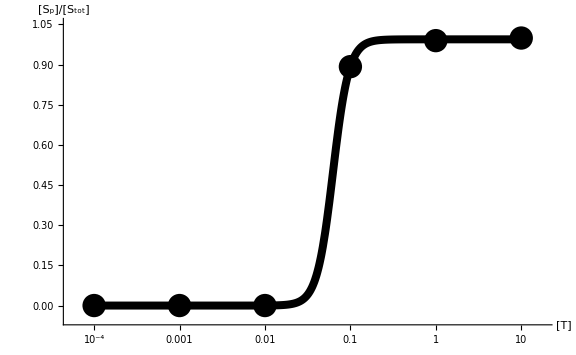

```mathematica
maxAndIndex[a_]:={#,First@SparseArray[UnitStep[a-#]]["AdjacencyLists"]}&@Max@a
usIndex=maxAndIndex[transPars[[11]]]//Last;
adIndex=maxAndIndex[transPars[[12]]]//Last;
stepNum=5;
maxPars=Flatten[Solve[Array[k,6]==pars[[usIndex]][[Range[6]]]]];totT=pars[[usIndex]][[7]];
Block[{tPer,ts,step,sol,ssthreshold},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[(Norm[df]<ssthreshold),{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k7[t]->10*k7[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
x4=Evaluate[x[4][ts-0.001]/.sol]/totS;k7t=Evaluate[(k7[ts-0.001])/.sol];
];
fittedHill=FindFit[Transpose@{k7t,x4},a+(b-a)*hillK/(hillK+x^(-n)),{a,b,hillK,n},x]
Show[LogLinearPlot[a+(b-a)*hillK/(hillK+x^(-n))/.fittedHill,{x,10^-4,10},(*Ticks->{Automatic,{0,0.5,1}},*) PlotRange->{-0.05,1.05}, AxesLabel->{"[T]","[S_p]/[S_tot]"},PlotTheme->"Monochrome",PlotStyle->{Thickness[0.01]}],ListLogLinearPlot[Transpose@{k7t,x4},PlotTheme->"Monochrome",PlotMarkers->{Automatic,24}], PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
```

```mathematica
usIndices=Flatten[Position[transPars[[11]],_?(#>0.8&)]];
adIndices=Flatten[Position[transPars[[12]],_?(#>0.1&)]];
usPars=pars[[usIndices]];adPars=pars[[adIndices]];
```

```mathematica
plotRange={{-6,6},{-6,6}};
```

```mathematica
data1=Transpose[{Log10[Transpose[usPars][[14]]],Log10[Transpose[usPars][[15]]]}];
data3=Transpose[{Log10[Transpose[adPars][[14]]],Log10[Transpose[adPars][[15]]]}];
```

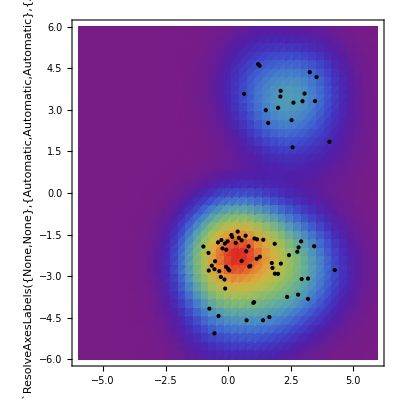

```mathematica
Show[SmoothDensityHistogram[data1,1,"PDF",ColorFunction->"Rainbow",Mesh->0,PlotRange->plotRange],Graphics[Point@data1],PlotRange->plotRange]
```

```mathematica
us=pars[[Flatten[Position[transPars[[11]],_?(#>0.7&)]]]];
usLow=us[[Flatten[Position[Transpose[us][[15]],_?(0.0001<#<0.01&)]]]];
usLowKm2=Flatten[usLow[[Ordering[Transpose[usLow][[11]],-1]]]];
usHigh=us[[Flatten[Position[Transpose[us][[15]],_?(100<#<10000&)]]]];
usHighKm2=Flatten[usHigh[[Ordering[Transpose[usHigh][[11]],-1]]]];
```

```mathematica
SetDirectory[NotebookDirectory[]];
kd=10;
des={-k[1]* x[1][t] *x[3][t]+k[2]* x[5][t]+k[3] *x[5][t]+k7[t]*kd-kd*x[1][t],-k[4]* x[2][t] *x[4][t]+k[5]* x[6][t]+k[6] *x[6][t],-k[1]* x[1][t] *x[3][t]+k[2] *x[5][t]+k[6]*x[6][t],
-k[4]*x[2][t]* x[4][t]+k[3]*x[5][t]+k[5]* x[6][t],
k[1]* x[1][t] *x[3][t]-k[2] *x[5][t]-k[3]* x[5][t],
k[4] *x[2][t]* x[4][t]-k[5] *x[6][t]-k[6] *x[6][t],0};

init={totK,totP,totS,0,0,0,1.*10^-4};(*init={tot[1],tot[2],tot[3],0.00001,0.00001,0.00001,totT,0.00001,0.00001};*)

vars=Array[x,6];AppendTo[vars,k7];
dvars=Thread[Derivative[1][vars]];

totK=0.0001;totP=0.1;totS=1;
stepNum=50;
```

```mathematica
Block[{ts,totT,xT,transAdToUsPars,usVsAd,maxPars},
maxPars=Solve[Array[k,6]==usLowKm2[[Range[6]]]];
Block[{ssthreshold},
totT=1.*10^(RandomReal[]*6-3);

Block[{tPer,step,us,ad,sol,i},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k7[t]->1.*10^(-4+0.1*step)}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];
p=Evaluate[x[2][ts-0.001]/.sol];
psp=Evaluate[x[6][ts-0.001]/.sol];
k=Evaluate[x[1][ts-0.001]/.sol];
ks=Evaluate[x[5][ts-0.001]/.sol];
];
];
];
];
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 2733.04 and t = 2745.52.

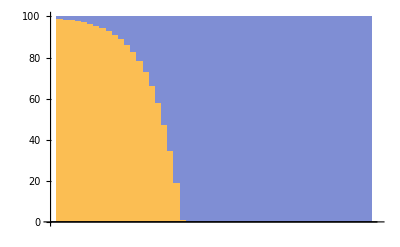

```mathematica
BarChart[Transpose[{p,psp}],ChartLayout->"Percentile"]
```

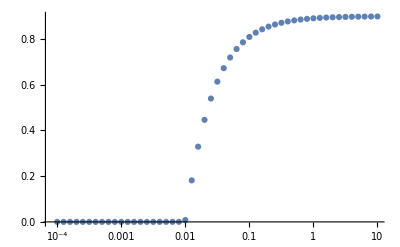

```mathematica
ListLogLinearPlot[Transpose[{Table[1.*10^(-4+0.1*i),{i,0,50}],x4}]]
```